```mathematica
full[n_Integer,first_Integer,second_Integer]:=full[n,first,second]=Piecewise[{{first, n==1}, {second, n==2}, {full[n-1,first,second]full[n-2,first,second], 0≤full[n-1,first,second]<10&&0≤full[n-2,first,second]<10}, {full[n-1,first,second]ones[full[n-2,first,second]], 0≤full[n-1]<10&&81≥full[n-2,first,second]≥10}, {tens[full[n-1,first,second]]ones[full[n-1]], 81≥full[n-1,first,second]≥10}}]
```

```mathematica
ones[n_Integer]:=Piecewise[{{n, n<10}, {n-tens[n], n≥10}}]
```

```mathematica
Clear[ones]
```

```mathematica
ones[n_Integer;0≥n≥81]:=Piecewise[{{n, n<10}, {n-10tens[n], n≥10}}]
```

```mathematica
Clear[ones]
```

```mathematica
tens[n_Integer; 0≥n≥81]:=Piecewise[{{0, n<10}, {Floor[n/10], n≥10}}]
```

```mathematica
ones[n_Integer;0≥n≥81]:=Piecewise[{{n, n<10}, {n-10tens[n], n≥10}}]
```

```mathematica
Clear[full]
```

```mathematica
full[n_Integer,first_Integer,second_Integer]:=full[n,first,second]=Piecewise[{{first, n==1}, {second, n==2}, {full[n-1,first,second]full[n-2,first,second], 0≤full[n-1,first,second]<10&&0≤full[n-2,first,second]<10}, {full[n-1,first,second]ones[full[n-2,first,second]], 0≤full[n-1]<10&&81≥full[n-2,first,second]≥10}, {tens[full[n-1,first,second]]ones[full[n-1]], 81≥full[n-1,first,second]≥10}}]
```

```mathematica
Flatten[
Table[
{j,k}->
Table[full[i,j,k], {i, 1, 20}],
{j,1,9},{k,1,9}],1]
```

```mathematica
1+1
```

```mathematica
1+1
```

```mathematica
tens[n_Integer; 0≥n≥81]:=Piecewise[{{0, n<10}, {Floor[n/10], n≥10}}]
```

```mathematica
ones[n_Integer;0≥n≥81]:=Piecewise[{{n, n<10}, {n-10tens[n], n≥10}}]
```

```mathematica
full[n_Integer,first_Integer,second_Integer]:=full[n,first,second]=Piecewise[{{first, n==1}, {second, n==2}, {full[n-1,first,second]full[n-2,first,second], 0≤full[n-1,first,second]<10&&0≤full[n-2,first,second]<10}, {full[n-1,first,second]ones[full[n-2,first,second]], 0≤full[n-1]<10&&81≥full[n-2,first,second]≥10}, {tens[full[n-1,first,second]]ones[full[n-1]], 81≥full[n-1,first,second]≥10}}]
```

```mathematica
full[1,1,2]
```

1

```mathematica
Table[full[i,1,2], {i, 1, 20}]
```

{f[1,1,2],f[2,1,2],f[3,1,2],f[4,1,2],f[5,1,2],f[6,1,2],f[7,1,2],f[8,1,2],f[9,1,2],f[10,1,2],f[11,1,2],f[12,1,2],f[13,1,2],f[14,1,2],f[15,1,2],f[16,1,2],f[17,1,2],f[18,1,2],f[19,1,2],f[20,1,2]}

```mathematica
1+1
```

2

```mathematica
full[n_Integer,first_Integer,second_Integer]:=full[n,first,second]=Piecewise[{{first, n==1}, {second, n==2}, {full[n-1,first,second]full[n-2,first,second], 0≤full[n-1,first,second]<10&&0≤full[n-2,first,second]<10}, {full[n-1,first,second]ones[full[n-2,first,second]], 0≤full[n-1,first,second]<10&&81≥full[n-2,first,second]≥10}, {tens[full[n-1,first,second]]ones[full[n-1,first,second]], 81≥full[n-1,first,second]≥10}}]
```

```mathematica
Flatten[
Table[
{j,k}->
Table[full[i,j,k], {i, 1, 20}],
{j,1,9},{k,1,9}],1]
```

```mathematica
tens[n_Integer; 0≥n≥81]:=Piecewise[{{0, n<10}, {Floor[n/10], n≥10}}]
```

```mathematica
ones[n_Integer;0≥n≥81]:=Piecewise[{{n, n<10}, {n-10tens[n], n≥10}}]
```

```mathematica
full[n_Integer,first_Integer,second_Integer]:=full[n,first,second]=Piecewise[{{first, n==1}, {second, n==2}, {full[n-1,first,second]full[n-2,first,second], 0≤full[n-1,first,second]<10&&0≤full[n-2,first,second]<10}, {full[n-1,first,second]ones[full[n-2,first,second]], 0≤full[n-1,first,second]<10&&81≥full[n-2,first,second]≥10}, {tens[full[n-1,first,second]]ones[full[n-1,first,second]], 81≥full[n-1,first,second]≥10}}]
```

```mathematica
Table[full[i,1,2],{i,1,3}]
```

{1,2,2}

```mathematica
Table[full[i,1,2],{i,1,10}]
```

{1,2,2,4,8,32,ones[32] tens[32],Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}],Piecewise[{{ones[32] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]) tens[32], 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]), 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&81≥ones[32] tens[32]≥10}, {ones[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]] tens[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]], 81≥(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])≥10}, {0, True}}],Piecewise[{{(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]) (Piecewise[{{ones[32] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]) tens[32], 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]), 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&81≥ones[32] tens[32]≥10}, {ones[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]] tens[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]], 81≥(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])≥10}, {0, True}}]), 0≤(Piecewise[{{ones[32] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]) tens[32], 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]), 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&81≥ones[32] tens[32]≥10}, {ones[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]] tens[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]], 81≥(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])≥10}, {0, True}}])<10&&0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10}, {ones[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]] (Piecewise[{{ones[32] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]) tens[32], 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]), 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&81≥ones[32] tens[32]≥10}, {ones[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]] tens[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]], 81≥(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])≥10}, {0, True}}]), 0≤(Piecewise[{{ones[32] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]) tens[32], 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]), 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&81≥ones[32] tens[32]≥10}, {ones[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]] tens[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]], 81≥(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])≥10}, {0, True}}])<10&&81≥(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])≥10}, {ones[Piecewise[{{ones[32] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]) tens[32], 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]), 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&81≥ones[32] tens[32]≥10}, {ones[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]] tens[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]], 81≥(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])≥10}, {0, True}}]] tens[Piecewise[{{ones[32] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]) tens[32], 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]), 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&81≥ones[32] tens[32]≥10}, {ones[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]] tens[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]], 81≥(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])≥10}, {0, True}}]], 81≥(Piecewise[{{ones[32] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]) tens[32], 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]), 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&81≥ones[32] tens[32]≥10}, {ones[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]] tens[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]], 81≥(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])≥10}, {0, True}}])≥10}, {0, True}}]}

```mathematica
1+1
```

2

```mathematica
ones
```

ones

```mathematica
ones[34]
```

ones[34]

```mathematica
ones[10]
```

ones[10]

```mathematica
Clear[ones]
```

```mathematica
Clear[tens]
```

```mathematica
f[n_Integer; Element[n,Integers]]:=n+n
```

```mathematica
f[2]
```

f[2]

```mathematica
Clear[f]
```

```mathematica
f[n_Integer]:=n+n/;Element[n,Integers]
```

```mathematica
f[4]
```

8

```mathematica
f[1.2]
```

f[1.2]

```mathematica
tens[n_Integer]:=Piecewise[{{0, n<10}, {Floor[n/10], n≥10}}]/;And[Element[n,Integers],0≥n≥81]
```

```mathematica
ones[n_Integer]:=Piecewise[{{n, n<10}, {n-10tens[n], n≥10}}]/;And[Element[n,Integers],0≥n≥81]
```

```mathematica
full[n_Integer,first_Integer,second_Integer]:=full[n,first,second]=Piecewise[{{first, n==1}, {second, n==2}, {full[n-1,first,second]full[n-2,first,second], 0≤full[n-1,first,second]<10&&0≤full[n-2,first,second]<10}, {full[n-1,first,second]ones[full[n-2,first,second]], 0≤full[n-1,first,second]<10&&81≥full[n-2,first,second]≥10}, {tens[full[n-1,first,second]]ones[full[n-1,first,second]], 81≥full[n-1,first,second]≥10}}]/;And[Element[n|first|second,Integers],0≤first≤ 9,0≤second≤9 ]
```

```mathematica
Table[full[i,1,2],{i,1,10}]
```

{1,2,2,4,8,32,ones[32] tens[32],Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}],Piecewise[{{ones[32] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]) tens[32], 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]), 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&81≥ones[32] tens[32]≥10}, {ones[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]] tens[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]], 81≥(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])≥10}, {0, True}}],Piecewise[{{(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]) (Piecewise[{{ones[32] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]) tens[32], 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]), 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&81≥ones[32] tens[32]≥10}, {ones[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]] tens[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]], 81≥(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])≥10}, {0, True}}]), 0≤(Piecewise[{{ones[32] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]) tens[32], 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]), 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&81≥ones[32] tens[32]≥10}, {ones[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]] tens[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]], 81≥(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])≥10}, {0, True}}])<10&&0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10}, {ones[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]] (Piecewise[{{ones[32] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]) tens[32], 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]), 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&81≥ones[32] tens[32]≥10}, {ones[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]] tens[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]], 81≥(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])≥10}, {0, True}}]), 0≤(Piecewise[{{ones[32] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]) tens[32], 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]), 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&81≥ones[32] tens[32]≥10}, {ones[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]] tens[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]], 81≥(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])≥10}, {0, True}}])<10&&81≥(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])≥10}, {ones[Piecewise[{{ones[32] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]) tens[32], 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]), 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&81≥ones[32] tens[32]≥10}, {ones[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]] tens[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]], 81≥(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])≥10}, {0, True}}]] tens[Piecewise[{{ones[32] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]) tens[32], 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]), 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&81≥ones[32] tens[32]≥10}, {ones[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]] tens[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]], 81≥(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])≥10}, {0, True}}]], 81≥(Piecewise[{{ones[32] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]) tens[32], 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] (Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]), 0≤(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])<10&&81≥ones[32] tens[32]≥10}, {ones[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]] tens[Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}]], 81≥(Piecewise[{{ones[32]^2 tens[32], 0≤ones[32] tens[32]<10}, {ones[ones[32] tens[32]] tens[ones[32] tens[32]], 81≥ones[32] tens[32]≥10}, {0, True}}])≥10}, {0, True}}])≥10}, {0, True}}]}

```mathematica
ones[32]
```

ones[32]

```mathematica
tens[32]
```

tens[32]

```mathematica
Clear[{ones,tens}]
```

Clear::ssym: {ones,tens} is not a symbol or a string.

```mathematica
Map[Clear,{ones,tens}]
```

{Null,Null}

```mathematica
tens[n_Integer]:=Piecewise[{{0, n<10}, {Floor[n/10], n≥10}}]/;And[Element[n,Integers],0≥n≥81]
```

```mathematica
tens[32]
```

tens[32]

```mathematica
Clear[32]
```

Clear::ssym: 32 is not a symbol or a string.

```mathematica
Clear[tens]
```

```mathematica
tens[n_Integer]:=Piecewise[{{0, n<10}, {Floor[n/10], n≥10}}]/;0≥n≥81
```

```mathematica
tens[32]
```

tens[32]

```mathematica
Clear[tens]
```

```mathematica
tens[n_Integer/; 0≥n≥81]:=Piecewise[{{0, n<10}, {Floor[n/10], n≥10}}]
```

```mathematica
tens[32]
```

tens[32]

```mathematica
Clear[tens]
```

```mathematica
tens[n_Integer]:=Piecewise[{{0, n<10}, {Floor[n/10], n≥10}}]
```

```mathematica
tens[32]
```

3

```mathematica
ones[n_Integer]:=Piecewise[{{n, n<10}, {n-10tens[n], n≥10}}]
```

```mathematica
ones[42]
```

2

```mathematica
ones[32]
```

2

```mathematica
Clear[full]
```

```mathematica
full[n_Integer,first_Integer,second_Integer]:=full[n,first,second]=Piecewise[{{first, n==1}, {second, n==2}, {full[n-1,first,second]full[n-2,first,second], 0≤full[n-1,first,second]<10&&0≤full[n-2,first,second]<10}, {full[n-1,first,second]ones[full[n-2,first,second]], 0≤full[n-1,first,second]<10&&81≥full[n-2,first,second]≥10}, {tens[full[n-1,first,second]]ones[full[n-1,first,second]], 81≥full[n-1,first,second]≥10}}]
```

```mathematica
Table[full[i,1,2],{i,1,10}]
```

{1,2,2,4,8,32,6,12,2,4}

```mathematica
Flatten[
Table[
{j,k}->
Table[full[i,j,k], {i, 1, 20}],
{j,1,9},{k,1,9}],1]
```

{{1,1}→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,2}→{1,2,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12},{1,3}→{1,3,3,9,27,14,4,16,6,36,18,8,64,24,8,32,6,12,2,4},{1,4}→{1,4,4,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12},{1,5}→{1,5,5,25,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,6}→{1,6,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4},{1,7}→{1,7,7,49,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2},{1,8}→{1,8,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6},{1,9}→{1,9,9,81,8,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4},{2,1}→{2,1,2,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6},{2,2}→{2,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2},{2,3}→{2,3,6,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8},{2,4}→{2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4},{2,5}→{2,5,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,6}→{2,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6},{2,7}→{2,7,14,4,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6},{2,8}→{2,8,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2},{2,9}→{2,9,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8,32},{3,1}→{3,1,3,3,9,27,14,4,16,6,36,18,8,64,24,8,32,6,12,2},{3,2}→{3,2,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32},{3,3}→{3,3,9,27,14,4,16,6,36,18,8,64,24,8,32,6,12,2,4,8},{3,4}→{3,4,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6},{3,5}→{3,5,15,5,25,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{3,6}→{3,6,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8,32},{3,7}→{3,7,21,2,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32},{3,8}→{3,8,24,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2},{3,9}→{3,9,27,14,4,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32},{4,1}→{4,1,4,4,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6},{4,2}→{4,2,8,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12},{4,3}→{4,3,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6},{4,4}→{4,4,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2},{4,5}→{4,5,20,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{4,6}→{4,6,24,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2},{4,7}→{4,7,28,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12},{4,8}→{4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8},{4,9}→{4,9,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8},{5,1}→{5,1,5,5,25,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,2}→{5,2,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,3}→{5,3,15,5,25,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,4}→{5,4,20,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,5}→{5,5,25,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,6}→{5,6,30,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,7}→{5,7,35,15,5,25,10,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,8}→{5,8,40,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,9}→{5,9,45,20,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{6,1}→{6,1,6,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2},{6,2}→{6,2,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6},{6,3}→{6,3,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8,32},{6,4}→{6,4,24,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2},{6,5}→{6,5,30,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{6,6}→{6,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8},{6,7}→{6,7,42,8,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6},{6,8}→{6,8,48,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4},{6,9}→{6,9,54,20,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{7,1}→{7,1,7,7,49,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12},{7,2}→{7,2,14,4,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6},{7,3}→{7,3,21,2,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32},{7,4}→{7,4,28,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12},{7,5}→{7,5,35,15,5,25,10,0,0,0,0,0,0,0,0,0,0,0,0,0},{7,6}→{7,6,42,8,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6},{7,7}→{7,7,49,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4},{7,8}→{7,8,56,30,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{7,9}→{7,9,63,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8},{8,1}→{8,1,8,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8,32},{8,2}→{8,2,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2},{8,3}→{8,3,24,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2},{8,4}→{8,4,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8},{8,5}→{8,5,40,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{8,6}→{8,6,48,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4},{8,7}→{8,7,56,30,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{8,8}→{8,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12},{8,9}→{8,9,72,14,4,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32},{9,1}→{9,1,9,9,81,8,8,64,24,8,32,6,12,2,4,8,32,6,12,2},{9,2}→{9,2,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8,32},{9,3}→{9,3,27,14,4,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32},{9,4}→{9,4,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8},{9,5}→{9,5,45,20,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{9,6}→{9,6,54,20,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{9,7}→{9,7,63,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8},{9,8}→{9,8,72,14,4,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32},{9,9}→{9,9,81,8,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8}}

```mathematica
{1,2,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12}
```

{1,2,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12}

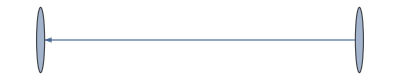

```mathematica
Graph[{{1,2}->2}]
```

```mathematica
FullForm[Out[46]]
```

Graph[List[List[1,2],2],List[DirectedEdge[List[1,2],2]]]

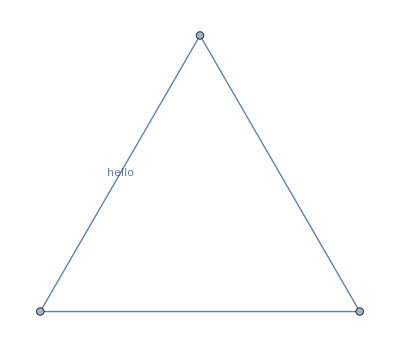
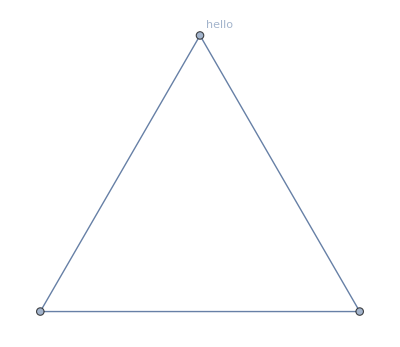

```mathematica
{Graph[{1<->2,2<->3,Labeled[3<->1,"hello"]}],Graph[{1,2,Labeled[3,"hello"]},{1<->2,2<->3,3<->1}]}
```

```mathematica
Graph[{1,2,Labeled[3,"hello"]},{1<->2,2<->3,3<->1}]
```

-Graphics-

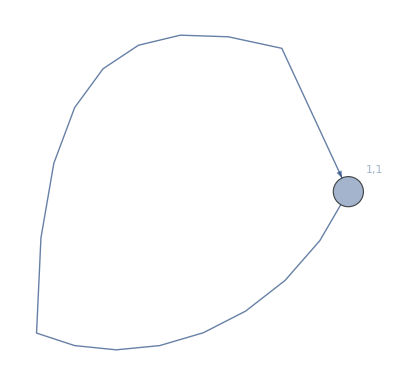

```mathematica
Graph[
{Labeled[1,"1,1"]},
{1->1}]
```

```mathematica
Graph[{
Labeled[1,"1,1"]
},{
1->1
}]
```

-Graphics-

```mathematica
f
```

f

```mathematica
Clear[f]
```

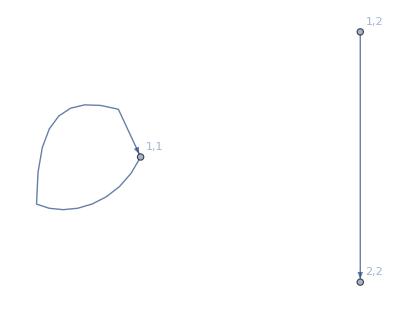

```mathematica
Graph[{
Labeled[f[1,1],"1,1"],
Labeled[f[1,2],"1,2"],
Labeled[f[2,2],"2,2"]
},{
f[1,1]->f[1,1],
f[1,2]->f[2,2]
}]
```

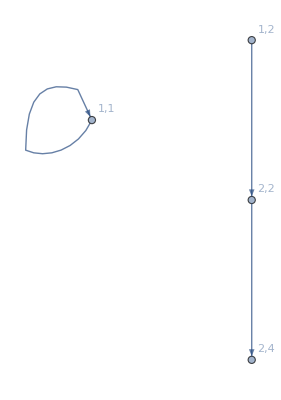

```mathematica
Graph[{
Labeled[f[1,1],"1,1"],
Labeled[f[1,2],"1,2"],
Labeled[f[2,2],"2,2"],
Labeled[f[2,4],"2,4"]
},{
f[1,1]->f[1,1],
f[1,2]->f[2,2],
f[2,2]->f[2,4]
}]
```

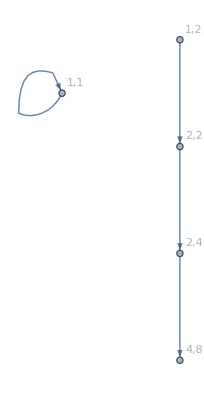

```mathematica
Graph[{
Labeled[f[1,1],"1,1"],
Labeled[f[1,2],"1,2"],
Labeled[f[2,2],"2,2"],
Labeled[f[2,4],"2,4"],
Labeled[f[4,8],"4,8"]
},{
f[1,1]->f[1,1],
f[1,2]->f[2,2],
f[2,2]->f[2,4],
f[2,4]->f[4,8]
}]
```

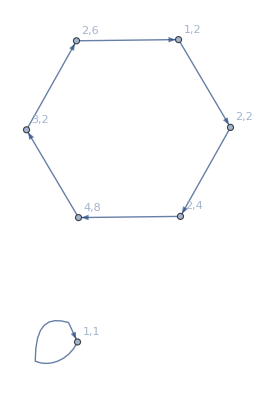

```mathematica
Graph[{
Labeled[f[1,1],"1,1"],
Labeled[f[1,2],"1,2"],
Labeled[f[2,2],"2,2"],
Labeled[f[2,4],"2,4"],
Labeled[f[4,8],"4,8"],
Labeled[f[3,2],"3,2"],
Labeled[f[2,6],"2,6"]
},{
f[1,1]->f[1,1],
f[1,2]->f[2,2],
f[2,2]->f[2,4],
f[2,4]->f[4,8],
f[4,8]->f[3,2],
f[3,2]->f[2,6],
f[2,6]->f[1,2]
}]
```

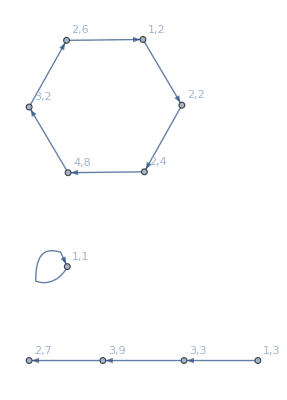

```mathematica
Graph[{
Labeled[f[1,1],"1,1"],
Labeled[f[1,2],"1,2"],
Labeled[f[2,2],"2,2"],
Labeled[f[2,4],"2,4"],
Labeled[f[4,8],"4,8"],
Labeled[f[3,2],"3,2"],
Labeled[f[2,6],"2,6"],
Labeled[f[1,3],"1,3"],
Labeled[f[3,3],"3,3"],
Labeled[f[3,9],"3,9"],
Labeled[f[2,7],"2,7"],
Labeled[f[1,4],"1,4"],
Labeled[f[4,4],"4,4"],
Labeled[f[1,6],"1,6"],
Labeled[f[6,6],"6,6"],
},{
f[1,1]->f[1,1],
f[1,2]->f[2,2],
f[2,2]->f[2,4],
f[2,4]->f[4,8],
f[4,8]->f[3,2],
f[3,2]->f[2,6],
f[2,6]->f[1,2],
f[1,3]->f[3,3],
f[3,3]->f[3,9],
f[3,9]->f[2,7]
}]
```

```mathematica
Table[Labeled[f[i,j],
StringJoin[ToString[i],",",ToString[j]]],{i, 0,9},{j,0,9}]
```

{{f[0,0]0,0,f[0,1]0,1,f[0,2]0,2,f[0,3]0,3,f[0,4]0,4,f[0,5]0,5,f[0,6]0,6,f[0,7]0,7,f[0,8]0,8,f[0,9]0,9},{f[1,0]1,0,f[1,1]1,1,f[1,2]1,2,f[1,3]1,3,f[1,4]1,4,f[1,5]1,5,f[1,6]1,6,f[1,7]1,7,f[1,8]1,8,f[1,9]1,9},{f[2,0]2,0,f[2,1]2,1,f[2,2]2,2,f[2,3]2,3,f[2,4]2,4,f[2,5]2,5,f[2,6]2,6,f[2,7]2,7,f[2,8]2,8,f[2,9]2,9},{f[3,0]3,0,f[3,1]3,1,f[3,2]3,2,f[3,3]3,3,f[3,4]3,4,f[3,5]3,5,f[3,6]3,6,f[3,7]3,7,f[3,8]3,8,f[3,9]3,9},{f[4,0]4,0,f[4,1]4,1,f[4,2]4,2,f[4,3]4,3,f[4,4]4,4,f[4,5]4,5,f[4,6]4,6,f[4,7]4,7,f[4,8]4,8,f[4,9]4,9},{f[5,0]5,0,f[5,1]5,1,f[5,2]5,2,f[5,3]5,3,f[5,4]5,4,f[5,5]5,5,f[5,6]5,6,f[5,7]5,7,f[5,8]5,8,f[5,9]5,9},{f[6,0]6,0,f[6,1]6,1,f[6,2]6,2,f[6,3]6,3,f[6,4]6,4,f[6,5]6,5,f[6,6]6,6,f[6,7]6,7,f[6,8]6,8,f[6,9]6,9},{f[7,0]7,0,f[7,1]7,1,f[7,2]7,2,f[7,3]7,3,f[7,4]7,4,f[7,5]7,5,f[7,6]7,6,f[7,7]7,7,f[7,8]7,8,f[7,9]7,9},{f[8,0]8,0,f[8,1]8,1,f[8,2]8,2,f[8,3]8,3,f[8,4]8,4,f[8,5]8,5,f[8,6]8,6,f[8,7]8,7,f[8,8]8,8,f[8,9]8,9},{f[9,0]9,0,f[9,1]9,1,f[9,2]9,2,f[9,3]9,3,f[9,4]9,4,f[9,5]9,5,f[9,6]9,6,f[9,7]9,7,f[9,8]9,8,f[9,9]9,9}}

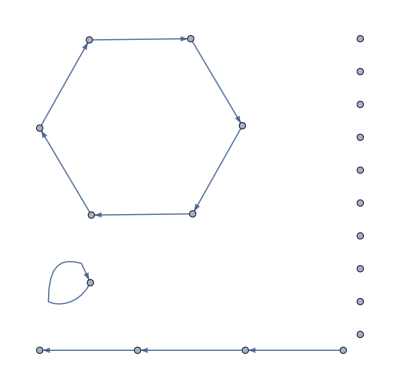

```mathematica
Graph[
Table[Labeled[f[i,j],
StringJoin[ToString[i],",",ToString[j]]],{i, 0,9},{j,0,9}],{
f[1,1]->f[1,1],
f[1,2]->f[2,2],
f[2,2]->f[2,4],
f[2,4]->f[4,8],
f[4,8]->f[3,2],
f[3,2]->f[2,6],
f[2,6]->f[1,2],
f[1,3]->f[3,3],
f[3,3]->f[3,9],
f[3,9]->f[2,7]
}]
```

```mathematica
Table[
Hold[Labeled[f[i,j],StringJoin[ToString[i],",",ToString[j]]]]
,{i, 0,9},{j,0,9}]
```

{{Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]]},{Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]]},{Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]]},{Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]]},{Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]]},{Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]]},{Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]]},{Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]]},{Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]]},{Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]],Hold[f[i,j]ToString[i]<>,<>ToString[j]]}}

```mathematica
FullForm[Out[69]]
```

List[List[Labeled[f[0,0],"0,0"],Labeled[f[0,1],"0,1"],Labeled[f[0,2],"0,2"],Labeled[f[0,3],"0,3"],Labeled[f[0,4],"0,4"],Labeled[f[0,5],"0,5"],Labeled[f[0,6],"0,6"],Labeled[f[0,7],"0,7"],Labeled[f[0,8],"0,8"],Labeled[f[0,9],"0,9"]],List[Labeled[f[1,0],"1,0"],Labeled[f[1,1],"1,1"],Labeled[f[1,2],"1,2"],Labeled[f[1,3],"1,3"],Labeled[f[1,4],"1,4"],Labeled[f[1,5],"1,5"],Labeled[f[1,6],"1,6"],Labeled[f[1,7],"1,7"],Labeled[f[1,8],"1,8"],Labeled[f[1,9],"1,9"]],List[Labeled[f[2,0],"2,0"],Labeled[f[2,1],"2,1"],Labeled[f[2,2],"2,2"],Labeled[f[2,3],"2,3"],Labeled[f[2,4],"2,4"],Labeled[f[2,5],"2,5"],Labeled[f[2,6],"2,6"],Labeled[f[2,7],"2,7"],Labeled[f[2,8],"2,8"],Labeled[f[2,9],"2,9"]],List[Labeled[f[3,0],"3,0"],Labeled[f[3,1],"3,1"],Labeled[f[3,2],"3,2"],Labeled[f[3,3],"3,3"],Labeled[f[3,4],"3,4"],Labeled[f[3,5],"3,5"],Labeled[f[3,6],"3,6"],Labeled[f[3,7],"3,7"],Labeled[f[3,8],"3,8"],Labeled[f[3,9],"3,9"]],List[Labeled[f[4,0],"4,0"],Labeled[f[4,1],"4,1"],Labeled[f[4,2],"4,2"],Labeled[f[4,3],"4,3"],Labeled[f[4,4],"4,4"],Labeled[f[4,5],"4,5"],Labeled[f[4,6],"4,6"],Labeled[f[4,7],"4,7"],Labeled[f[4,8],"4,8"],Labeled[f[4,9],"4,9"]],List[Labeled[f[5,0],"5,0"],Labeled[f[5,1],"5,1"],Labeled[f[5,2],"5,2"],Labeled[f[5,3],"5,3"],Labeled[f[5,4],"5,4"],Labeled[f[5,5],"5,5"],Labeled[f[5,6],"5,6"],Labeled[f[5,7],"5,7"],Labeled[f[5,8],"5,8"],Labeled[f[5,9],"5,9"]],List[Labeled[f[6,0],"6,0"],Labeled[f[6,1],"6,1"],Labeled[f[6,2],"6,2"],Labeled[f[6,3],"6,3"],Labeled[f[6,4],"6,4"],Labeled[f[6,5],"6,5"],Labeled[f[6,6],"6,6"],Labeled[f[6,7],"6,7"],Labeled[f[6,8],"6,8"],Labeled[f[6,9],"6,9"]],List[Labeled[f[7,0],"7,0"],Labeled[f[7,1],"7,1"],Labeled[f[7,2],"7,2"],Labeled[f[7,3],"7,3"],Labeled[f[7,4],"7,4"],Labeled[f[7,5],"7,5"],Labeled[f[7,6],"7,6"],Labeled[f[7,7],"7,7"],Labeled[f[7,8],"7,8"],Labeled[f[7,9],"7,9"]],List[Labeled[f[8,0],"8,0"],Labeled[f[8,1],"8,1"],Labeled[f[8,2],"8,2"],Labeled[f[8,3],"8,3"],Labeled[f[8,4],"8,4"],Labeled[f[8,5],"8,5"],Labeled[f[8,6],"8,6"],Labeled[f[8,7],"8,7"],Labeled[f[8,8],"8,8"],Labeled[f[8,9],"8,9"]],List[Labeled[f[9,0],"9,0"],Labeled[f[9,1],"9,1"],Labeled[f[9,2],"9,2"],Labeled[f[9,3],"9,3"],Labeled[f[9,4],"9,4"],Labeled[f[9,5],"9,5"],Labeled[f[9,6],"9,6"],Labeled[f[9,7],"9,7"],Labeled[f[9,8],"9,8"],Labeled[f[9,9],"9,9"]]]

```mathematica
Flatten[
Table[
Labeled[f[i,j],
StringJoin[ToString[i],",",ToString[j]]],{i, 0,9},{j,0,9}],1]
```

{f[0,0]0,0,f[0,1]0,1,f[0,2]0,2,f[0,3]0,3,f[0,4]0,4,f[0,5]0,5,f[0,6]0,6,f[0,7]0,7,f[0,8]0,8,f[0,9]0,9,f[1,0]1,0,f[1,1]1,1,f[1,2]1,2,f[1,3]1,3,f[1,4]1,4,f[1,5]1,5,f[1,6]1,6,f[1,7]1,7,f[1,8]1,8,f[1,9]1,9,f[2,0]2,0,f[2,1]2,1,f[2,2]2,2,f[2,3]2,3,f[2,4]2,4,f[2,5]2,5,f[2,6]2,6,f[2,7]2,7,f[2,8]2,8,f[2,9]2,9,f[3,0]3,0,f[3,1]3,1,f[3,2]3,2,f[3,3]3,3,f[3,4]3,4,f[3,5]3,5,f[3,6]3,6,f[3,7]3,7,f[3,8]3,8,f[3,9]3,9,f[4,0]4,0,f[4,1]4,1,f[4,2]4,2,f[4,3]4,3,f[4,4]4,4,f[4,5]4,5,f[4,6]4,6,f[4,7]4,7,f[4,8]4,8,f[4,9]4,9,f[5,0]5,0,f[5,1]5,1,f[5,2]5,2,f[5,3]5,3,f[5,4]5,4,f[5,5]5,5,f[5,6]5,6,f[5,7]5,7,f[5,8]5,8,f[5,9]5,9,f[6,0]6,0,f[6,1]6,1,f[6,2]6,2,f[6,3]6,3,f[6,4]6,4,f[6,5]6,5,f[6,6]6,6,f[6,7]6,7,f[6,8]6,8,f[6,9]6,9,f[7,0]7,0,f[7,1]7,1,f[7,2]7,2,f[7,3]7,3,f[7,4]7,4,f[7,5]7,5,f[7,6]7,6,f[7,7]7,7,f[7,8]7,8,f[7,9]7,9,f[8,0]8,0,f[8,1]8,1,f[8,2]8,2,f[8,3]8,3,f[8,4]8,4,f[8,5]8,5,f[8,6]8,6,f[8,7]8,7,f[8,8]8,8,f[8,9]8,9,f[9,0]9,0,f[9,1]9,1,f[9,2]9,2,f[9,3]9,3,f[9,4]9,4,f[9,5]9,5,f[9,6]9,6,f[9,7]9,7,f[9,8]9,8,f[9,9]9,9}

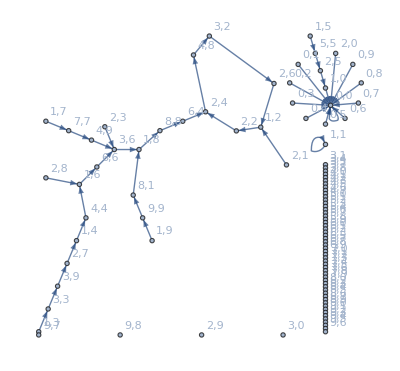

```mathematica
Graph[
{f[0,0]"0,0",f[0,1]"0,1",f[0,2]"0,2",f[0,3]"0,3",f[0,4]"0,4",f[0,5]"0,5",f[0,6]"0,6",f[0,7]"0,7",f[0,8]"0,8",f[0,9]"0,9",f[1,0]"1,0",f[1,1]"1,1",f[1,2]"1,2",f[1,3]"1,3",f[1,4]"1,4",f[1,5]"1,5",f[1,6]"1,6",f[1,7]"1,7",f[1,8]"1,8",f[1,9]"1,9",f[2,0]"2,0",f[2,1]"2,1",f[2,2]"2,2",f[2,3]"2,3",f[2,4]"2,4",f[2,5]"2,5",f[2,6]"2,6",f[2,7]"2,7",f[2,8]"2,8",f[2,9]"2,9",f[3,0]"3,0",f[3,1]"3,1",f[3,2]"3,2",f[3,3]"3,3",f[3,4]"3,4",f[3,5]"3,5",f[3,6]"3,6",f[3,7]"3,7",f[3,8]"3,8",f[3,9]"3,9",f[4,0]"4,0",f[4,1]"4,1",f[4,2]"4,2",f[4,3]"4,3",f[4,4]"4,4",f[4,5]"4,5",f[4,6]"4,6",f[4,7]"4,7",f[4,8]"4,8",f[4,9]"4,9",f[5,0]"5,0",f[5,1]"5,1",f[5,2]"5,2",f[5,3]"5,3",f[5,4]"5,4",f[5,5]"5,5",f[5,6]"5,6",f[5,7]"5,7",f[5,8]"5,8",f[5,9]"5,9",f[6,0]"6,0",f[6,1]"6,1",f[6,2]"6,2",f[6,3]"6,3",f[6,4]"6,4",f[6,5]"6,5",f[6,6]"6,6",f[6,7]"6,7",f[6,8]"6,8",f[6,9]"6,9",f[7,0]"7,0",f[7,1]"7,1",f[7,2]"7,2",f[7,3]"7,3",f[7,4]"7,4",f[7,5]"7,5",f[7,6]"7,6",f[7,7]"7,7",f[7,8]"7,8",f[7,9]"7,9",f[8,0]"8,0",f[8,1]"8,1",f[8,2]"8,2",f[8,3]"8,3",f[8,4]"8,4",f[8,5]"8,5",f[8,6]"8,6",f[8,7]"8,7",f[8,8]"8,8",f[8,9]"8,9",f[9,0]"9,0",f[9,1]"9,1",f[9,2]"9,2",f[9,3]"9,3",f[9,4]"9,4",f[9,5]"9,5",f[9,6]"9,6",f[9,7]"9,7",f[9,8]"9,8",f[9,9]"9,9"},{
f[0,0]->f[0,0],
f[0,1]->f[0,0],
f[0,2]->f[0,0],
f[0,3]->f[0,0],
f[0,4]->f[0,0],
f[0,5]->f[0,0],
f[0,6]->f[0,0],
f[0,7]->f[0,0],
f[0,8]->f[0,0],
f[0,9]->f[0,0],
f[1,1]->f[1,1],
f[1,2]->f[2,2],
f[2,2]->f[2,4],
f[2,4]->f[4,8],
f[4,8]->f[3,2],
f[3,2]->f[2,6],
f[2,6]->f[1,2],
f[1,3]->f[3,3],
f[3,3]->f[3,9],
f[3,9]->f[2,7],
f[2,7]->f[1,4],
f[1,4]->f[4,4],
f[4,4]-> f[1,6],
f[1,6]->f[6,6],
f[6,6]->f[3,6],
f[3,6]->f[1,8],
f[1,8]->f[8,8],
f[8,8]->f[6,4],
f[6,4]->f[2,4],
f[1,5]->f[5,5],
f[5,5]->f[2,5],
f[2,5]->f[1,0],
f[1,0]->f[0,0],
f[1,7]->f[7,7],
f[7,7]->f[4,9],
f[4,9]->f[3,6],
f[1,9]->f[9,9],
f[9,9]->f[8,1],
f[8,1]->f[1,8],
f[2,0]->f[0,0],
f[2,1]->f[1,2],
f[2,3]->f[3,6],
f[2,8]->f[1,6]
},GraphLayout->"RadialEmbedding"]
```

```mathematica
f[{a_Integer,b_Integer}]:=Piecewise[{{{b,a b}, 9≥a b≥0}, {{tens[a b], ones[a b]}, 10≥a b≥81}}]/;And[0≥a≥9,0≥b≥9]
```

```mathematica
f[{2,5}]
```

f[{2,5}]

```mathematica
Clear[f]
```

```mathematica
f[{a_Integer,b_Integer}]:=Piecewise[{{{b,a b}, 9≥a b≥0}, {{tens[a b], ones[a b]}, 10≥a b≥81}}]
```

```mathematica
f[{1,2}]
```

{2,2}

```mathematica
Nest[f,{1,2},2]
```

{2,4}

```mathematica
Table[
Nest[f,{1,2},i],{i, 1, 10}]
```

{{2,2},{2,4},{4,8},0,f[0],f[f[0]],f[f[f[0]]],f[f[f[f[0]]]],f[f[f[f[f[0]]]]],f[f[f[f[f[f[0]]]]]]}

```mathematica
f[{4,8}]
```

0

```mathematica
{tens[a b], ones[a b]}/.{a->4,b->8}
```

{3,2}

```mathematica
f[{4,8}]
```

0

```mathematica
Clear[f]
```

```mathematica
f[{a_Integer,b_Integer}]:=Piecewise[{{{b,a b}, 9≥a b≥0}, {{tens[a b], ones[a b]}, 81≥a b≥10}}]
```

```mathematica
Table[
Nest[f,{1,2},i],{i, 1, 10}]
```

{{2,2},{2,4},{4,8},{3,2},{2,6},{1,2},{2,2},{2,4},{4,8},{3,2}}

```mathematica
Table[{i,j}->f[{i,j}], {i, 0, 9}, {j, 0, 9}]
```

{{{0,0}→{0,0},{0,1}→{1,0},{0,2}→{2,0},{0,3}→{3,0},{0,4}→{4,0},{0,5}→{5,0},{0,6}→{6,0},{0,7}→{7,0},{0,8}→{8,0},{0,9}→{9,0}},{{1,0}→{0,0},{1,1}→{1,1},{1,2}→{2,2},{1,3}→{3,3},{1,4}→{4,4},{1,5}→{5,5},{1,6}→{6,6},{1,7}→{7,7},{1,8}→{8,8},{1,9}→{9,9}},{{2,0}→{0,0},{2,1}→{1,2},{2,2}→{2,4},{2,3}→{3,6},{2,4}→{4,8},{2,5}→{1,0},{2,6}→{1,2},{2,7}→{1,4},{2,8}→{1,6},{2,9}→{1,8}},{{3,0}→{0,0},{3,1}→{1,3},{3,2}→{2,6},{3,3}→{3,9},{3,4}→{1,2},{3,5}→{1,5},{3,6}→{1,8},{3,7}→{2,1},{3,8}→{2,4},{3,9}→{2,7}},{{4,0}→{0,0},{4,1}→{1,4},{4,2}→{2,8},{4,3}→{1,2},{4,4}→{1,6},{4,5}→{2,0},{4,6}→{2,4},{4,7}→{2,8},{4,8}→{3,2},{4,9}→{3,6}},{{5,0}→{0,0},{5,1}→{1,5},{5,2}→{1,0},{5,3}→{1,5},{5,4}→{2,0},{5,5}→{2,5},{5,6}→{3,0},{5,7}→{3,5},{5,8}→{4,0},{5,9}→{4,5}},{{6,0}→{0,0},{6,1}→{1,6},{6,2}→{1,2},{6,3}→{1,8},{6,4}→{2,4},{6,5}→{3,0},{6,6}→{3,6},{6,7}→{4,2},{6,8}→{4,8},{6,9}→{5,4}},{{7,0}→{0,0},{7,1}→{1,7},{7,2}→{1,4},{7,3}→{2,1},{7,4}→{2,8},{7,5}→{3,5},{7,6}→{4,2},{7,7}→{4,9},{7,8}→{5,6},{7,9}→{6,3}},{{8,0}→{0,0},{8,1}→{1,8},{8,2}→{1,6},{8,3}→{2,4},{8,4}→{3,2},{8,5}→{4,0},{8,6}→{4,8},{8,7}→{5,6},{8,8}→{6,4},{8,9}→{7,2}},{{9,0}→{0,0},{9,1}→{1,9},{9,2}→{1,8},{9,3}→{2,7},{9,4}→{3,6},{9,5}→{4,5},{9,6}→{5,4},{9,7}→{6,3},{9,8}→{7,2},{9,9}→{8,1}}}

```mathematica
Table[g[{i,j}]->g[f[{i,j}]], {i, 0, 9}, {j, 0, 9}]
```

{{g[{0,0}]→g[{0,0}],g[{0,1}]→g[{1,0}],g[{0,2}]→g[{2,0}],g[{0,3}]→g[{3,0}],g[{0,4}]→g[{4,0}],g[{0,5}]→g[{5,0}],g[{0,6}]→g[{6,0}],g[{0,7}]→g[{7,0}],g[{0,8}]→g[{8,0}],g[{0,9}]→g[{9,0}]},{g[{1,0}]→g[{0,0}],g[{1,1}]→g[{1,1}],g[{1,2}]→g[{2,2}],g[{1,3}]→g[{3,3}],g[{1,4}]→g[{4,4}],g[{1,5}]→g[{5,5}],g[{1,6}]→g[{6,6}],g[{1,7}]→g[{7,7}],g[{1,8}]→g[{8,8}],g[{1,9}]→g[{9,9}]},{g[{2,0}]→g[{0,0}],g[{2,1}]→g[{1,2}],g[{2,2}]→g[{2,4}],g[{2,3}]→g[{3,6}],g[{2,4}]→g[{4,8}],g[{2,5}]→g[{1,0}],g[{2,6}]→g[{1,2}],g[{2,7}]→g[{1,4}],g[{2,8}]→g[{1,6}],g[{2,9}]→g[{1,8}]},{g[{3,0}]→g[{0,0}],g[{3,1}]→g[{1,3}],g[{3,2}]→g[{2,6}],g[{3,3}]→g[{3,9}],g[{3,4}]→g[{1,2}],g[{3,5}]→g[{1,5}],g[{3,6}]→g[{1,8}],g[{3,7}]→g[{2,1}],g[{3,8}]→g[{2,4}],g[{3,9}]→g[{2,7}]},{g[{4,0}]→g[{0,0}],g[{4,1}]→g[{1,4}],g[{4,2}]→g[{2,8}],g[{4,3}]→g[{1,2}],g[{4,4}]→g[{1,6}],g[{4,5}]→g[{2,0}],g[{4,6}]→g[{2,4}],g[{4,7}]→g[{2,8}],g[{4,8}]→g[{3,2}],g[{4,9}]→g[{3,6}]},{g[{5,0}]→g[{0,0}],g[{5,1}]→g[{1,5}],g[{5,2}]→g[{1,0}],g[{5,3}]→g[{1,5}],g[{5,4}]→g[{2,0}],g[{5,5}]→g[{2,5}],g[{5,6}]→g[{3,0}],g[{5,7}]→g[{3,5}],g[{5,8}]→g[{4,0}],g[{5,9}]→g[{4,5}]},{g[{6,0}]→g[{0,0}],g[{6,1}]→g[{1,6}],g[{6,2}]→g[{1,2}],g[{6,3}]→g[{1,8}],g[{6,4}]→g[{2,4}],g[{6,5}]→g[{3,0}],g[{6,6}]→g[{3,6}],g[{6,7}]→g[{4,2}],g[{6,8}]→g[{4,8}],g[{6,9}]→g[{5,4}]},{g[{7,0}]→g[{0,0}],g[{7,1}]→g[{1,7}],g[{7,2}]→g[{1,4}],g[{7,3}]→g[{2,1}],g[{7,4}]→g[{2,8}],g[{7,5}]→g[{3,5}],g[{7,6}]→g[{4,2}],g[{7,7}]→g[{4,9}],g[{7,8}]→g[{5,6}],g[{7,9}]→g[{6,3}]},{g[{8,0}]→g[{0,0}],g[{8,1}]→g[{1,8}],g[{8,2}]→g[{1,6}],g[{8,3}]→g[{2,4}],g[{8,4}]→g[{3,2}],g[{8,5}]→g[{4,0}],g[{8,6}]→g[{4,8}],g[{8,7}]→g[{5,6}],g[{8,8}]→g[{6,4}],g[{8,9}]→g[{7,2}]},{g[{9,0}]→g[{0,0}],g[{9,1}]→g[{1,9}],g[{9,2}]→g[{1,8}],g[{9,3}]→g[{2,7}],g[{9,4}]→g[{3,6}],g[{9,5}]→g[{4,5}],g[{9,6}]→g[{5,4}],g[{9,7}]→g[{6,3}],g[{9,8}]→g[{7,2}],g[{9,9}]→g[{8,1}]}}

```mathematica
Graph[
Table[g[{i,j}]->g[f[{i,j}]], {i, 0, 9}, {j, 0, 9}]]
```

Graph[{{g[{0,0}]→g[{0,0}],g[{0,1}]→g[{1,0}],g[{0,2}]→g[{2,0}],g[{0,3}]→g[{3,0}],g[{0,4}]→g[{4,0}],g[{0,5}]→g[{5,0}],g[{0,6}]→g[{6,0}],g[{0,7}]→g[{7,0}],g[{0,8}]→g[{8,0}],g[{0,9}]→g[{9,0}]},{g[{1,0}]→g[{0,0}],g[{1,1}]→g[{1,1}],g[{1,2}]→g[{2,2}],g[{1,3}]→g[{3,3}],g[{1,4}]→g[{4,4}],g[{1,5}]→g[{5,5}],g[{1,6}]→g[{6,6}],g[{1,7}]→g[{7,7}],g[{1,8}]→g[{8,8}],g[{1,9}]→g[{9,9}]},{g[{2,0}]→g[{0,0}],g[{2,1}]→g[{1,2}],g[{2,2}]→g[{2,4}],g[{2,3}]→g[{3,6}],g[{2,4}]→g[{4,8}],g[{2,5}]→g[{1,0}],g[{2,6}]→g[{1,2}],g[{2,7}]→g[{1,4}],g[{2,8}]→g[{1,6}],g[{2,9}]→g[{1,8}]},{g[{3,0}]→g[{0,0}],g[{3,1}]→g[{1,3}],g[{3,2}]→g[{2,6}],g[{3,3}]→g[{3,9}],g[{3,4}]→g[{1,2}],g[{3,5}]→g[{1,5}],g[{3,6}]→g[{1,8}],g[{3,7}]→g[{2,1}],g[{3,8}]→g[{2,4}],g[{3,9}]→g[{2,7}]},{g[{4,0}]→g[{0,0}],g[{4,1}]→g[{1,4}],g[{4,2}]→g[{2,8}],g[{4,3}]→g[{1,2}],g[{4,4}]→g[{1,6}],g[{4,5}]→g[{2,0}],g[{4,6}]→g[{2,4}],g[{4,7}]→g[{2,8}],g[{4,8}]→g[{3,2}],g[{4,9}]→g[{3,6}]},{g[{5,0}]→g[{0,0}],g[{5,1}]→g[{1,5}],g[{5,2}]→g[{1,0}],g[{5,3}]→g[{1,5}],g[{5,4}]→g[{2,0}],g[{5,5}]→g[{2,5}],g[{5,6}]→g[{3,0}],g[{5,7}]→g[{3,5}],g[{5,8}]→g[{4,0}],g[{5,9}]→g[{4,5}]},{g[{6,0}]→g[{0,0}],g[{6,1}]→g[{1,6}],g[{6,2}]→g[{1,2}],g[{6,3}]→g[{1,8}],g[{6,4}]→g[{2,4}],g[{6,5}]→g[{3,0}],g[{6,6}]→g[{3,6}],g[{6,7}]→g[{4,2}],g[{6,8}]→g[{4,8}],g[{6,9}]→g[{5,4}]},{g[{7,0}]→g[{0,0}],g[{7,1}]→g[{1,7}],g[{7,2}]→g[{1,4}],g[{7,3}]→g[{2,1}],g[{7,4}]→g[{2,8}],g[{7,5}]→g[{3,5}],g[{7,6}]→g[{4,2}],g[{7,7}]→g[{4,9}],g[{7,8}]→g[{5,6}],g[{7,9}]→g[{6,3}]},{g[{8,0}]→g[{0,0}],g[{8,1}]→g[{1,8}],g[{8,2}]→g[{1,6}],g[{8,3}]→g[{2,4}],g[{8,4}]→g[{3,2}],g[{8,5}]→g[{4,0}],g[{8,6}]→g[{4,8}],g[{8,7}]→g[{5,6}],g[{8,8}]→g[{6,4}],g[{8,9}]→g[{7,2}]},{g[{9,0}]→g[{0,0}],g[{9,1}]→g[{1,9}],g[{9,2}]→g[{1,8}],g[{9,3}]→g[{2,7}],g[{9,4}]→g[{3,6}],g[{9,5}]→g[{4,5}],g[{9,6}]→g[{5,4}],g[{9,7}]→g[{6,3}],g[{9,8}]→g[{7,2}],g[{9,9}]→g[{8,1}]}}]

```mathematica
Flatten[
Table[g[{i,j}]->g[f[{i,j}]], {i, 0, 9}, {j, 0, 9}],1]
```

{g[{0,0}]→g[{0,0}],g[{0,1}]→g[{1,0}],g[{0,2}]→g[{2,0}],g[{0,3}]→g[{3,0}],g[{0,4}]→g[{4,0}],g[{0,5}]→g[{5,0}],g[{0,6}]→g[{6,0}],g[{0,7}]→g[{7,0}],g[{0,8}]→g[{8,0}],g[{0,9}]→g[{9,0}],g[{1,0}]→g[{0,0}],g[{1,1}]→g[{1,1}],g[{1,2}]→g[{2,2}],g[{1,3}]→g[{3,3}],g[{1,4}]→g[{4,4}],g[{1,5}]→g[{5,5}],g[{1,6}]→g[{6,6}],g[{1,7}]→g[{7,7}],g[{1,8}]→g[{8,8}],g[{1,9}]→g[{9,9}],g[{2,0}]→g[{0,0}],g[{2,1}]→g[{1,2}],g[{2,2}]→g[{2,4}],g[{2,3}]→g[{3,6}],g[{2,4}]→g[{4,8}],g[{2,5}]→g[{1,0}],g[{2,6}]→g[{1,2}],g[{2,7}]→g[{1,4}],g[{2,8}]→g[{1,6}],g[{2,9}]→g[{1,8}],g[{3,0}]→g[{0,0}],g[{3,1}]→g[{1,3}],g[{3,2}]→g[{2,6}],g[{3,3}]→g[{3,9}],g[{3,4}]→g[{1,2}],g[{3,5}]→g[{1,5}],g[{3,6}]→g[{1,8}],g[{3,7}]→g[{2,1}],g[{3,8}]→g[{2,4}],g[{3,9}]→g[{2,7}],g[{4,0}]→g[{0,0}],g[{4,1}]→g[{1,4}],g[{4,2}]→g[{2,8}],g[{4,3}]→g[{1,2}],g[{4,4}]→g[{1,6}],g[{4,5}]→g[{2,0}],g[{4,6}]→g[{2,4}],g[{4,7}]→g[{2,8}],g[{4,8}]→g[{3,2}],g[{4,9}]→g[{3,6}],g[{5,0}]→g[{0,0}],g[{5,1}]→g[{1,5}],g[{5,2}]→g[{1,0}],g[{5,3}]→g[{1,5}],g[{5,4}]→g[{2,0}],g[{5,5}]→g[{2,5}],g[{5,6}]→g[{3,0}],g[{5,7}]→g[{3,5}],g[{5,8}]→g[{4,0}],g[{5,9}]→g[{4,5}],g[{6,0}]→g[{0,0}],g[{6,1}]→g[{1,6}],g[{6,2}]→g[{1,2}],g[{6,3}]→g[{1,8}],g[{6,4}]→g[{2,4}],g[{6,5}]→g[{3,0}],g[{6,6}]→g[{3,6}],g[{6,7}]→g[{4,2}],g[{6,8}]→g[{4,8}],g[{6,9}]→g[{5,4}],g[{7,0}]→g[{0,0}],g[{7,1}]→g[{1,7}],g[{7,2}]→g[{1,4}],g[{7,3}]→g[{2,1}],g[{7,4}]→g[{2,8}],g[{7,5}]→g[{3,5}],g[{7,6}]→g[{4,2}],g[{7,7}]→g[{4,9}],g[{7,8}]→g[{5,6}],g[{7,9}]→g[{6,3}],g[{8,0}]→g[{0,0}],g[{8,1}]→g[{1,8}],g[{8,2}]→g[{1,6}],g[{8,3}]→g[{2,4}],g[{8,4}]→g[{3,2}],g[{8,5}]→g[{4,0}],g[{8,6}]→g[{4,8}],g[{8,7}]→g[{5,6}],g[{8,8}]→g[{6,4}],g[{8,9}]→g[{7,2}],g[{9,0}]→g[{0,0}],g[{9,1}]→g[{1,9}],g[{9,2}]→g[{1,8}],g[{9,3}]→g[{2,7}],g[{9,4}]→g[{3,6}],g[{9,5}]→g[{4,5}],g[{9,6}]→g[{5,4}],g[{9,7}]→g[{6,3}],g[{9,8}]→g[{7,2}],g[{9,9}]→g[{8,1}]}

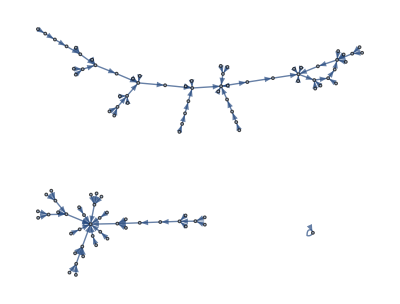

```mathematica
Graph[
Flatten[
Table[g[{i,j}]->g[f[{i,j}]], {i, 0, 9}, {j, 0, 9}],1]]
```

```mathematica
Clear[f]
```

```mathematica
f[{a_Integer,b_Integer}]:=Piecewise[{{{0,0}, Or[a==0,b==0]}, {{b,a b}, 9≥a b≥0}, {{tens[a b], ones[a b]}, 10≥a b≥81}}]
```

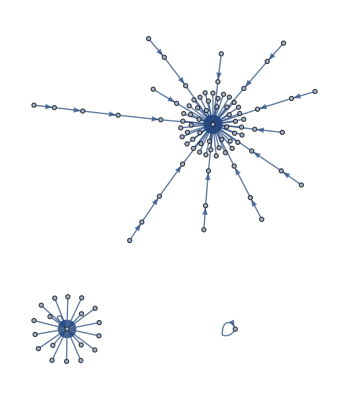

```mathematica
Graph[
Flatten[
Table[g[{i,j}]->g[f[{i,j}]], {i, 0, 9}, {j, 0, 9}],1]]
```

```mathematica
Flatten[
Table[g[{i,j}]->g[f[{i,j}]], {i, 0, 9}, {j, 0, 9}],1]
```

{g[{0,0}]→g[{0,0}],g[{0,1}]→g[{0,0}],g[{0,2}]→g[{0,0}],g[{0,3}]→g[{0,0}],g[{0,4}]→g[{0,0}],g[{0,5}]→g[{0,0}],g[{0,6}]→g[{0,0}],g[{0,7}]→g[{0,0}],g[{0,8}]→g[{0,0}],g[{0,9}]→g[{0,0}],g[{1,0}]→g[{0,0}],g[{1,1}]→g[{1,1}],g[{1,2}]→g[{2,2}],g[{1,3}]→g[{3,3}],g[{1,4}]→g[{4,4}],g[{1,5}]→g[{5,5}],g[{1,6}]→g[{6,6}],g[{1,7}]→g[{7,7}],g[{1,8}]→g[{8,8}],g[{1,9}]→g[{9,9}],g[{2,0}]→g[{0,0}],g[{2,1}]→g[{1,2}],g[{2,2}]→g[{2,4}],g[{2,3}]→g[{3,6}],g[{2,4}]→g[{4,8}],g[{2,5}]→g[0],g[{2,6}]→g[0],g[{2,7}]→g[0],g[{2,8}]→g[0],g[{2,9}]→g[0],g[{3,0}]→g[{0,0}],g[{3,1}]→g[{1,3}],g[{3,2}]→g[{2,6}],g[{3,3}]→g[{3,9}],g[{3,4}]→g[0],g[{3,5}]→g[0],g[{3,6}]→g[0],g[{3,7}]→g[0],g[{3,8}]→g[0],g[{3,9}]→g[0],g[{4,0}]→g[{0,0}],g[{4,1}]→g[{1,4}],g[{4,2}]→g[{2,8}],g[{4,3}]→g[0],g[{4,4}]→g[0],g[{4,5}]→g[0],g[{4,6}]→g[0],g[{4,7}]→g[0],g[{4,8}]→g[0],g[{4,9}]→g[0],g[{5,0}]→g[{0,0}],g[{5,1}]→g[{1,5}],g[{5,2}]→g[0],g[{5,3}]→g[0],g[{5,4}]→g[0],g[{5,5}]→g[0],g[{5,6}]→g[0],g[{5,7}]→g[0],g[{5,8}]→g[0],g[{5,9}]→g[0],g[{6,0}]→g[{0,0}],g[{6,1}]→g[{1,6}],g[{6,2}]→g[0],g[{6,3}]→g[0],g[{6,4}]→g[0],g[{6,5}]→g[0],g[{6,6}]→g[0],g[{6,7}]→g[0],g[{6,8}]→g[0],g[{6,9}]→g[0],g[{7,0}]→g[{0,0}],g[{7,1}]→g[{1,7}],g[{7,2}]→g[0],g[{7,3}]→g[0],g[{7,4}]→g[0],g[{7,5}]→g[0],g[{7,6}]→g[0],g[{7,7}]→g[0],g[{7,8}]→g[0],g[{7,9}]→g[0],g[{8,0}]→g[{0,0}],g[{8,1}]→g[{1,8}],g[{8,2}]→g[0],g[{8,3}]→g[0],g[{8,4}]→g[0],g[{8,5}]→g[0],g[{8,6}]→g[0],g[{8,7}]→g[0],g[{8,8}]→g[0],g[{8,9}]→g[0],g[{9,0}]→g[{0,0}],g[{9,1}]→g[{1,9}],g[{9,2}]→g[0],g[{9,3}]→g[0],g[{9,4}]→g[0],g[{9,5}]→g[0],g[{9,6}]→g[0],g[{9,7}]→g[0],g[{9,8}]→g[0],g[{9,9}]→g[0]}

```mathematica
Clear[f]
```

```mathematica
f[{a_Integer,b_Integer}]:=Piecewise[{{{0,0}, Or[a==0,b==0]}, {{b,a b}, 9≥a b≥0}, {{tens[a b], ones[a b]}, 81≥a b≥10}}]
```

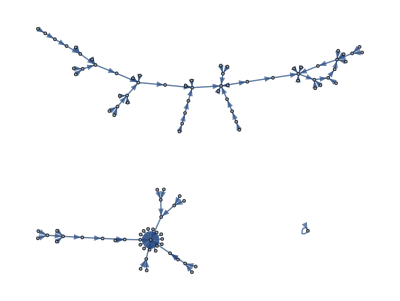

```mathematica
Graph[
Flatten[
Table[g[{i,j}]->g[f[{i,j}]], {i, 0, 9}, {j, 0, 9}],1]]
```

```mathematica
Flatten[
Table[
Labeled[g[{i,j}],
StringJoin[ToString[i],",",ToString[j]]],
{i, 0, 9}, {j, 0, 9}],1]
```

{g[{0,0}]0,0,g[{0,1}]0,1,g[{0,2}]0,2,g[{0,3}]0,3,g[{0,4}]0,4,g[{0,5}]0,5,g[{0,6}]0,6,g[{0,7}]0,7,g[{0,8}]0,8,g[{0,9}]0,9,g[{1,0}]1,0,g[{1,1}]1,1,g[{1,2}]1,2,g[{1,3}]1,3,g[{1,4}]1,4,g[{1,5}]1,5,g[{1,6}]1,6,g[{1,7}]1,7,g[{1,8}]1,8,g[{1,9}]1,9,g[{2,0}]2,0,g[{2,1}]2,1,g[{2,2}]2,2,g[{2,3}]2,3,g[{2,4}]2,4,g[{2,5}]2,5,g[{2,6}]2,6,g[{2,7}]2,7,g[{2,8}]2,8,g[{2,9}]2,9,g[{3,0}]3,0,g[{3,1}]3,1,g[{3,2}]3,2,g[{3,3}]3,3,g[{3,4}]3,4,g[{3,5}]3,5,g[{3,6}]3,6,g[{3,7}]3,7,g[{3,8}]3,8,g[{3,9}]3,9,g[{4,0}]4,0,g[{4,1}]4,1,g[{4,2}]4,2,g[{4,3}]4,3,g[{4,4}]4,4,g[{4,5}]4,5,g[{4,6}]4,6,g[{4,7}]4,7,g[{4,8}]4,8,g[{4,9}]4,9,g[{5,0}]5,0,g[{5,1}]5,1,g[{5,2}]5,2,g[{5,3}]5,3,g[{5,4}]5,4,g[{5,5}]5,5,g[{5,6}]5,6,g[{5,7}]5,7,g[{5,8}]5,8,g[{5,9}]5,9,g[{6,0}]6,0,g[{6,1}]6,1,g[{6,2}]6,2,g[{6,3}]6,3,g[{6,4}]6,4,g[{6,5}]6,5,g[{6,6}]6,6,g[{6,7}]6,7,g[{6,8}]6,8,g[{6,9}]6,9,g[{7,0}]7,0,g[{7,1}]7,1,g[{7,2}]7,2,g[{7,3}]7,3,g[{7,4}]7,4,g[{7,5}]7,5,g[{7,6}]7,6,g[{7,7}]7,7,g[{7,8}]7,8,g[{7,9}]7,9,g[{8,0}]8,0,g[{8,1}]8,1,g[{8,2}]8,2,g[{8,3}]8,3,g[{8,4}]8,4,g[{8,5}]8,5,g[{8,6}]8,6,g[{8,7}]8,7,g[{8,8}]8,8,g[{8,9}]8,9,g[{9,0}]9,0,g[{9,1}]9,1,g[{9,2}]9,2,g[{9,3}]9,3,g[{9,4}]9,4,g[{9,5}]9,5,g[{9,6}]9,6,g[{9,7}]9,7,g[{9,8}]9,8,g[{9,9}]9,9}

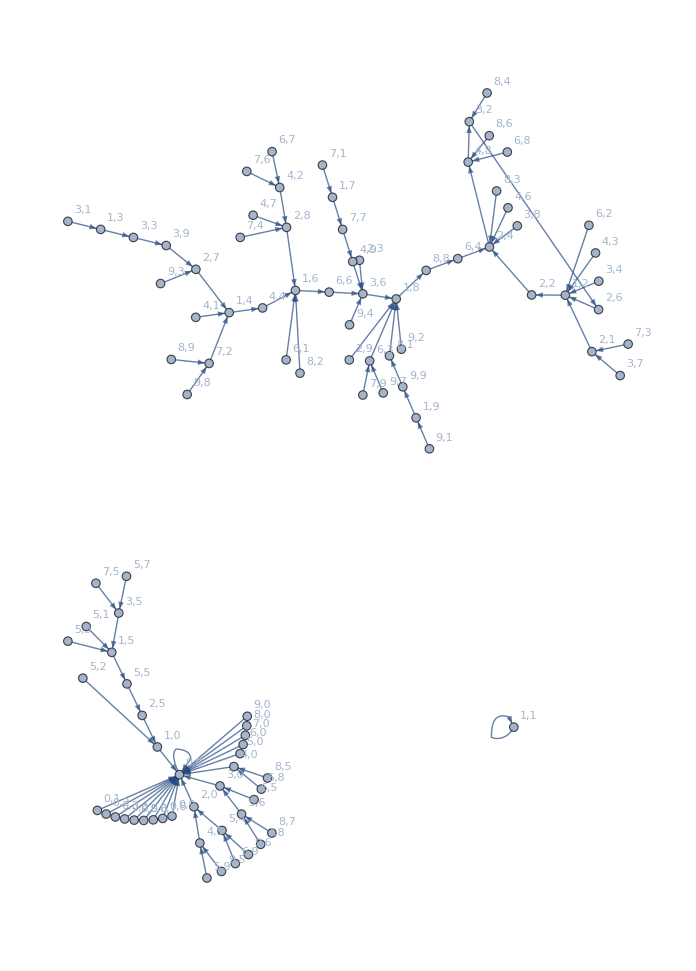

```mathematica
Graph[
Flatten[
Table[
Labeled[g[{i,j}],
StringJoin[ToString[i],",",ToString[j]]],
{i, 0, 9}, {j, 0, 9}],1],
Flatten[
Table[g[{i,j}]->g[f[{i,j}]], {i, 0, 9}, {j, 0, 9}],1],
GraphLayout->"RadialEmbedding"]
```

```mathematica
Clear[f]
```

```mathematica
f[{a_Integer,b_Integer}]:=Piecewise[{{{0,0}, And[a==0,b==0]}, {{b,0}, b==0}, {{b,a b}, 9≥a b≥0}, {{tens[a b], ones[a b]}, 81≥a b≥10}}]
```

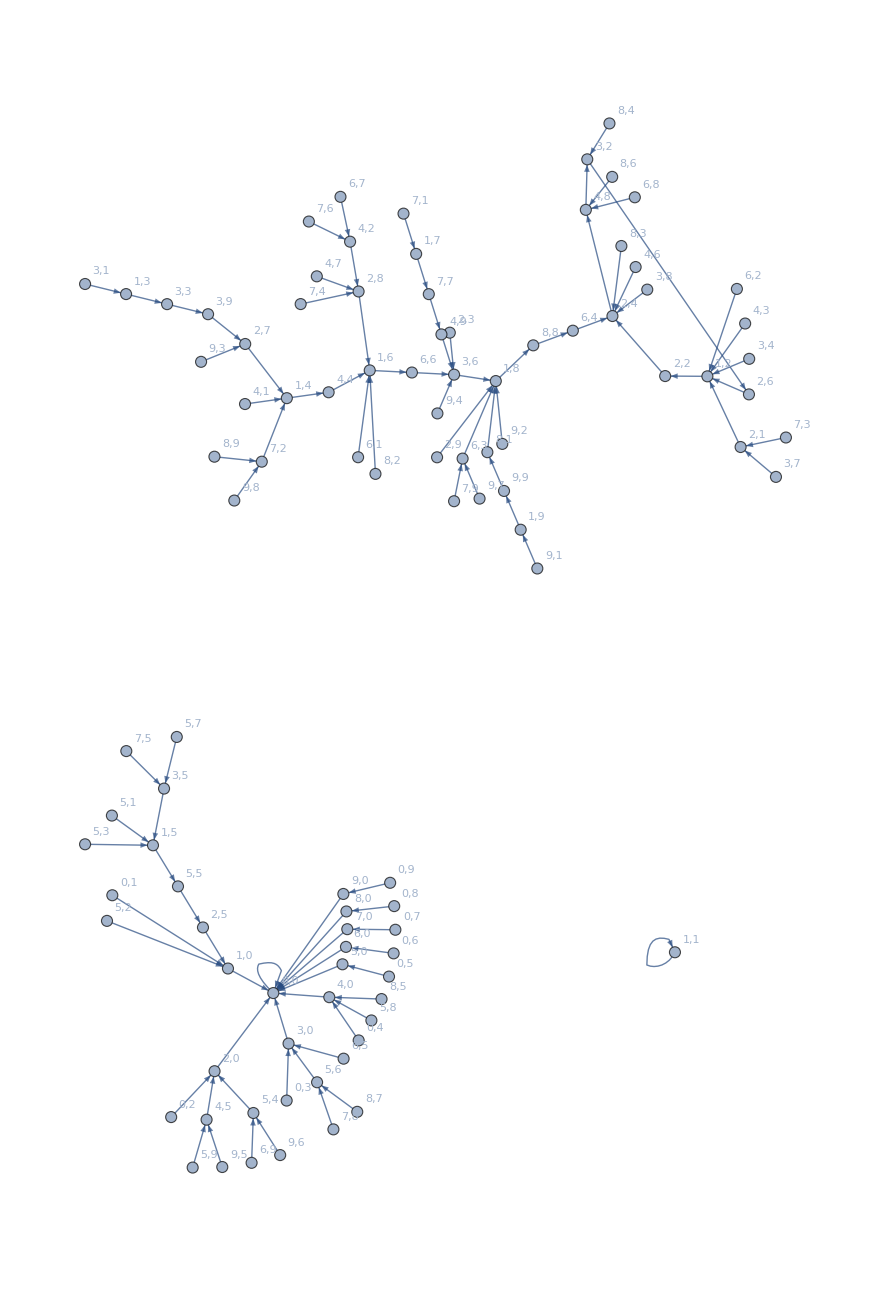

```mathematica
Graph[
Flatten[
Table[
Labeled[g[{i,j}],
StringJoin[ToString[i],",",ToString[j]]],
{i, 0, 9}, {j, 0, 9}],1],
Flatten[
Table[g[{i,j}]->g[f[{i,j}]], {i, 0, 9}, {j, 0, 9}],1],
GraphLayout->"RadialEmbedding"]
```

FindShortestPath::inv: The argument 13 in FindShortestPath[Graph[<100>, <100>], 13, 84] is not a valid vertex.

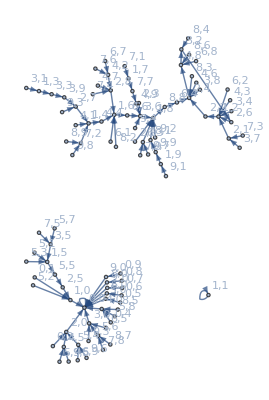
FindShortestPath[-Graphics-,13,84]

```mathematica
FindShortestPath[%123,13,84]
```

```mathematica
FindShortestPath[Out[123],g[{3,1}],g[{2,2}]]
```

{g[{3,1}],g[{1,3}],g[{3,3}],g[{3,9}],g[{2,7}],g[{1,4}],g[{4,4}],g[{1,6}],g[{6,6}],g[{3,6}],g[{1,8}],g[{8,8}],g[{6,4}],g[{2,4}],g[{4,8}],g[{3,2}],g[{2,6}],g[{1,2}],g[{2,2}]}

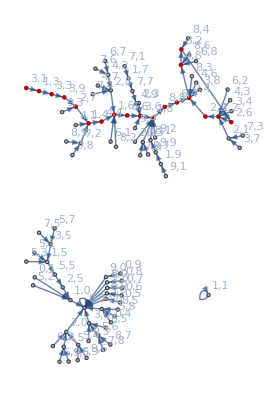

```mathematica
HighlightGraph[Graph[{g[{0,0}],g[{0,1}],g[{0,2}],g[{0,3}],g[{0,4}],g[{0,5}],g[{0,6}],g[{0,7}],g[{0,8}],g[{0,9}],g[{1,0}],g[{1,1}],g[{1,2}],g[{1,3}],g[{1,4}],g[{1,5}],g[{1,6}],g[{1,7}],g[{1,8}],g[{1,9}],g[{2,0}],g[{2,1}],g[{2,2}],g[{2,3}],g[{2,4}],g[{2,5}],g[{2,6}],g[{2,7}],g[{2,8}],g[{2,9}],g[{3,0}],g[{3,1}],g[{3,2}],g[{3,3}],g[{3,4}],g[{3,5}],g[{3,6}],g[{3,7}],g[{3,8}],g[{3,9}],g[{4,0}],g[{4,1}],g[{4,2}],g[{4,3}],g[{4,4}],g[{4,5}],g[{4,6}],g[{4,7}],g[{4,8}],g[{4,9}],g[{5,0}],g[{5,1}],g[{5,2}],g[{5,3}],g[{5,4}],g[{5,5}],g[{5,6}],g[{5,7}],g[{5,8}],g[{5,9}],g[{6,0}],g[{6,1}],g[{6,2}],g[{6,3}],g[{6,4}],g[{6,5}],g[{6,6}],g[{6,7}],g[{6,8}],g[{6,9}],g[{7,0}],g[{7,1}],g[{7,2}],g[{7,3}],g[{7,4}],g[{7,5}],g[{7,6}],g[{7,7}],g[{7,8}],g[{7,9}],g[{8,0}],g[{8,1}],g[{8,2}],g[{8,3}],g[{8,4}],g[{8,5}],g[{8,6}],g[{8,7}],g[{8,8}],g[{8,9}],g[{9,0}],g[{9,1}],g[{9,2}],g[{9,3}],g[{9,4}],g[{9,5}],g[{9,6}],g[{9,7}],g[{9,8}],g[{9,9}]},{{{1,1},{2,11},{3,21},{4,31},{5,41},{6,51},{7,61},{8,71},{9,81},{10,91},{11,1},{12,12},{13,23},{14,34},{15,45},{16,56},{17,67},{18,78},{19,89},{20,100},{21,1},{22,13},{23,25},{24,37},{25,49},{26,11},{27,13},{28,15},{29,17},{30,19},{31,1},{32,14},{33,27},{34,40},{35,13},{36,16},{37,19},{38,22},{39,25},{40,28},{41,1},{42,15},{43,29},{44,13},{45,17},{46,21},{47,25},{48,29},{49,33},{50,37},{51,1},{52,16},{53,11},{54,16},{55,21},{56,26},{57,31},{58,36},{59,41},{60,46},{61,1},{62,17},{63,13},{64,19},{65,25},{66,31},{67,37},{68,43},{69,49},{70,55},{71,1},{72,18},{73,15},{74,22},{75,29},{76,36},{77,43},{78,50},{79,57},{80,64},{81,1},{82,19},{83,17},{84,25},{85,33},{86,41},{87,49},{88,57},{89,65},{90,73},{91,1},{92,20},{93,19},{94,28},{95,37},{96,46},{97,55},{98,64},{99,73},{100,82}},Null},{GraphLayout->"RadialEmbedding",VertexLabels->{g[{5,0}]->"5,0",g[{2,0}]->"2,0",g[{2,7}]->"2,7",g[{4,8}]->"4,8",g[{9,9}]->"9,9",g[{8,1}]->"8,1",g[{6,6}]->"6,6",g[{1,3}]->"1,3",g[{8,5}]->"8,5",g[{2,5}]->"2,5",g[{3,8}]->"3,8",g[{0,4}]->"0,4",g[{7,3}]->"7,3",g[{4,9}]->"4,9",g[{0,6}]->"0,6",g[{0,5}]->"0,5",g[{9,4}]->"9,4",g[{4,5}]->"4,5",g[{1,4}]->"1,4",g[{1,5}]->"1,5",g[{5,3}]->"5,3",g[{9,5}]->"9,5",g[{3,3}]->"3,3",g[{1,8}]->"1,8",g[{2,6}]->"2,6",g[{9,0}]->"9,0",g[{8,2}]->"8,2",g[{4,2}]->"4,2",g[{6,7}]->"6,7",g[{8,3}]->"8,3",g[{1,2}]->"1,2",g[{6,4}]->"6,4",g[{5,2}]->"5,2",g[{7,5}]->"7,5",g[{0,0}]->"0,0",g[{3,0}]->"3,0",g[{8,0}]->"8,0",g[{9,8}]->"9,8",g[{3,1}]->"3,1",g[{4,6}]->"4,6",g[{1,1}]->"1,1",g[{7,9}]->"7,9",g[{8,4}]->"8,4",g[{0,8}]->"0,8",g[{1,7}]->"1,7",g[{2,3}]->"2,3",g[{1,9}]->"1,9",g[{1,0}]->"1,0",g[{6,9}]->"6,9",g[{0,9}]->"0,9",g[{6,8}]->"6,8",g[{5,1}]->"5,1",g[{1,6}]->"1,6",g[{6,1}]->"6,1",g[{9,6}]->"9,6",g[{4,0}]->"4,0",g[{2,4}]->"2,4",g[{2,2}]->"2,2",g[{7,2}]->"7,2",g[{7,7}]->"7,7",g[{4,7}]->"4,7",g[{3,4}]->"3,4",g[{3,9}]->"3,9",g[{9,3}]->"9,3",g[{8,7}]->"8,7",g[{8,6}]->"8,6",g[{7,1}]->"7,1",g[{8,9}]->"8,9",g[{7,8}]->"7,8",g[{6,2}]->"6,2",g[{9,2}]->"9,2",g[{3,5}]->"3,5",g[{2,9}]->"2,9",g[{5,6}]->"5,6",g[{7,4}]->"7,4",g[{5,9}]->"5,9",g[{6,3}]->"6,3",g[{5,8}]->"5,8",g[{4,1}]->"4,1",g[{8,8}]->"8,8",g[{3,2}]->"3,2",g[{4,3}]->"4,3",g[{0,7}]->"0,7",g[{2,1}]->"2,1",g[{6,5}]->"6,5",g[{7,6}]->"7,6",g[{2,8}]->"2,8",g[{3,7}]->"3,7",g[{5,7}]->"5,7",g[{9,7}]->"9,7",g[{7,0}]->"7,0",g[{5,4}]->"5,4",g[{9,1}]->"9,1",g[{0,2}]->"0,2",g[{3,6}]->"3,6",g[{0,1}]->"0,1",g[{5,5}]->"5,5",g[{6,0}]->"6,0",g[{0,3}]->"0,3",g[{4,4}]->"4,4"}}],PathGraph[{g[{3,1}],g[{1,3}],g[{3,3}],g[{3,9}],g[{2,7}],g[{1,4}],g[{4,4}],g[{1,6}],g[{6,6}],g[{3,6}],g[{1,8}],g[{8,8}],g[{6,4}],g[{2,4}],g[{4,8}],g[{3,2}],g[{2,6}],g[{1,2}],g[{2,2}]}]]
```

```mathematica
Length[Out[125]]
```

19